```mathematica
∫_1^10 (ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)ⅆx
```

1/2 (-Erf[(-10+μ)/(√2 σ)]+Erf[(-1+μ)/(√2 σ)])

```mathematica
Integrate[(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ),x]
```

1/2 Erf[(x-μ)/(√2 σ)]

```mathematica
Plot[Erf[x],{x,-5,5}]
```

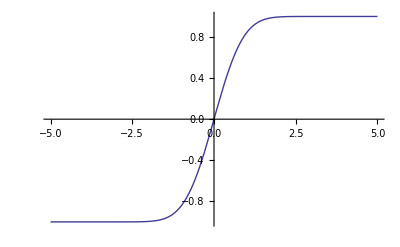

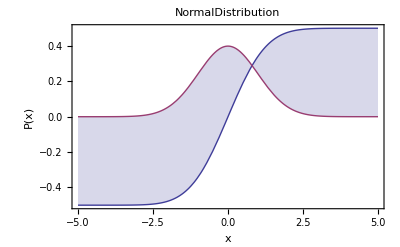

```mathematica
Plot[{1/2 Erf[(x-0)/(√2 1)],(ⅇ^(-(x-0)^2/(2 1^2)))/(√(2 π) 1)},{x,-5,5},Filling->{1->{2}},Frame->True,FrameLabel->{x,P[x]},PlotLabel->NormalDistribution,LabelStyle->Purple]
```

```mathematica
Erf[z]
gives the error function erf(z).
```

Erf[z]
gives the error function erf z.

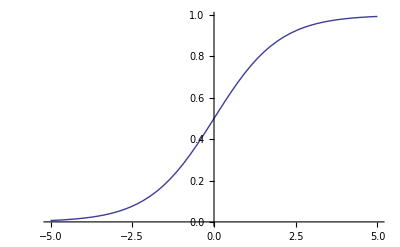

```mathematica
Plot[CDF[LogisticDistribution[0,1],x],{x,-5,5}]
```

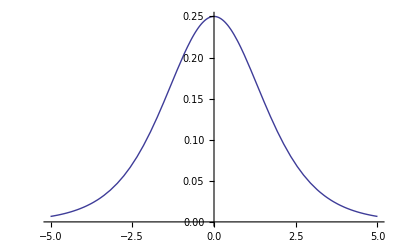

```mathematica
Plot[PDF[LogisticDistribution[0,1],x],{x,-5,5}]
```

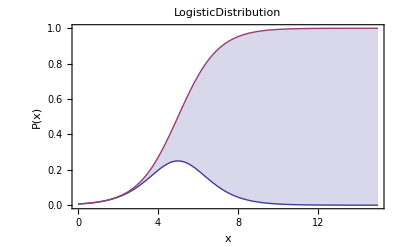

```mathematica
Plot[{PDF[LogisticDistribution[5,1],x],CDF[LogisticDistribution[5,1],x]},{x,0,15},Filling->{1->{2}},Frame->True,FrameLabel->{x,P[x]},PlotLabel->LogisticDistribution,LabelStyle->Purple]
```

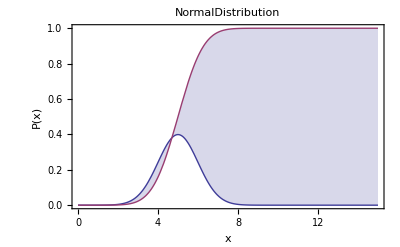

```mathematica
Plot[{PDF[NormalDistribution[5,1],x],CDF[NormalDistribution[5,1],x]},{x,0,15},Filling->{1->{2}},Frame->True,FrameLabel->{x,P[x]},PlotLabel->NormalDistribution,LabelStyle->Purple]
```

```mathematica
PDF[LogisticDistribution[μ,β],x]
```

ⅇ^(-(x-μ)/β)/((1+ⅇ^(-(x-μ)/β))^2 β)

```mathematica
CDF[LogisticDistribution[μ,β],x]
```

1/(1+ⅇ^(-(x-μ)/β))

```mathematica
CDF[NormalDistribution[μ,β],x]
```

1/2 (1+Erf[(x-μ)/(√2 β)])

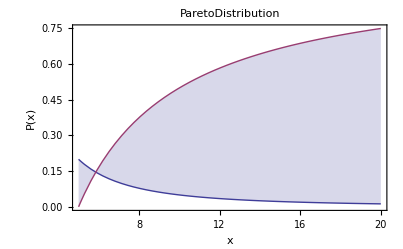

```mathematica
Plot[{PDF[ParetoDistribution[5,1],x],CDF[ParetoDistribution[5,1],x]},{x,5,20},Filling->{1->{2}},Frame->True,FrameLabel->{x,P[x]},PlotLabel->ParetoDistribution,LabelStyle->Purple]
```

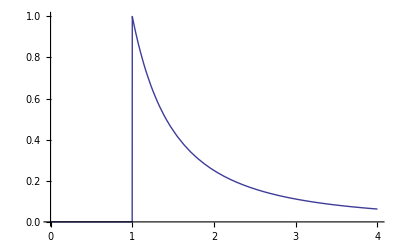

```mathematica
Plot[PDF[ParetoDistribution[1,1],x],{x,0,4}]
```